More about Pure Functions

We’ve seen how to make lists and arrays with Table. There’s also a way to do it using pure functions—with Array.

Generate a 10-element array with an abstract function f:

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

Use a pure function to generate a list of the first 10 squares:

```mathematica
Array[#^2&,10]
```

{1,4,9,16,25,36,49,64,81,100}

Table can give the same result, though you have to introduce the variable n:

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Array[f,4] makes a single list of 4 elements. Array[f,{3,4}] makes a 3×4 array.

Make a list of length 3, each of whose elements is a list of length 4:

```mathematica
Array[f,{3,4}]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2],f[2,3],f[2,4]},{f[3,1],f[3,2],f[3,3],f[3,4]}}

Display it in a grid:

```mathematica
Array[f,{3,4}]//Grid
```

f[1,1] | f[1,2] | f[1,3] | f[1,4]
f[2,1] | f[2,2] | f[2,3] | f[2,4]
f[3,1] | f[3,2] | f[3,3] | f[3,4]

If the function is Times, Array makes a multiplication table:

```mathematica
Grid[Array[Times,{5,5}]]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

What if we want to use a pure function in place of Times? When we compute Times[3,4], we say that Times is applied to two arguments. (In Times[3,4,5], Times is applied to three arguments, etc.) In a pure function, #1 represents the first argument, #2 the second argument and so on.

#1 represents the first argument, #2 the second argument:

```mathematica
f[#1,#2]&[55,66]
```

f[55,66]

#1 always picks out the first argument, and #2 the second argument:

```mathematica
f[#2,#1,{#2,#2,#1}]&[55,66]
```

f[66,55,{66,66,55}]

Now we can use #1 and #2 inside a function in Array.

Use a pure function to make a multiplication table:

```mathematica
Array[#1*#2&,{5,5}]//Grid
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

Use a different pure function that puts in x whenever the numbers are equal:

```mathematica
Array[If[#1==#2,x,#1*#2]&,{5,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

Here’s the equivalent computation with Table:

```mathematica
Table[If[i==j,x,i*j],{i,5},{j,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

Now that we’ve discussed pure functions with more than one argument, we’re in a position to talk about FoldList. You can think of FoldList as a 2-argument generalization of NestList.

NestList takes a single function, say f, and successively nests it:

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

It’s easier to understand when the function we use is Framed:

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

NestList just keeps on applying a function to whatever result it got before. FoldList does the same, except that it also “folds in” a new element each time.

Here’s FoldList with an abstract function f:

```mathematica
FoldList[f,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

Including Framed makes it a little easier to see what’s going on:

```mathematica
FoldList[Framed[f[#1,#2]]&,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

At first, this may look complicated and obscure, and it might seem hard to imagine how it could be useful. But actually, it’s very useful, and surprisingly common in real programs.

FoldList is good for progressively accumulating things. Let’s start with a simple case: progressively adding up numbers.

At each step FoldList folds in another element (#2), adding it to the result so far (#1):

```mathematica
FoldList[#1+#2&,0,{1,1,1,2,0,0}]
```

{0,1,2,3,5,5,5}

Here’s the computation it’s doing:

```mathematica
{0,0+1,(0+1)+1,((0+1)+1)+1,(((0+1)+1)+1)+2,((((0+1)+1)+1)+2)+0,(((((0+1)+1)+1)+2)+0)+0}
```

{0,1,2,3,5,5,5}

Or equivalently:

```mathematica
{0,0+1,0+1+1,0+1+1+1,0+1+1+1+2,0+1+1+1+2+0,0+1+1+1+2+0+0}
```

{0,1,2,3,5,5,5}

It may be easier to see what’s going on with symbols:

```mathematica
FoldList[#1+#2&,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

Of course, this case is simple enough that you don’t actually need a pure function:

```mathematica
FoldList[Plus,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

A classic use of FoldList is to successively “fold in” digits to reconstruct a number from its list of digits.

Successively construct a number from its digits, starting the folding process with its first digit:

```mathematica
FoldList[10#1+#2&,{8,7,6,1,2,3,9,8,7}]
```

{8,87,876,8761,87612,876123,8761239,87612398,876123987}

Finally, let’s use FoldList to “fold in” progressive images from a list, at each point adding them with ImageAdd to the image obtained so far.

Progressively “fold in” images from a list, combining them with ImageAdd:

```mathematica
FoldList[ImageAdd,
{ -Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics- }]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The concept of FoldList is not at first the easiest to understand. But when you’ve got it, you’ve learned an extremely powerful functional programming technique that’s an example of the kind of elegant abstraction possible in the Wolfram Language.

Vocabulary

Array[ f,n] |   | make an array by applying a function 
Array[ f,{m,n}] |   | make an array in 2D
FoldList[ f,x,list] |   | successively apply a function, folding in elements of a list

"6 Exercises Available"
"with 1 extras" | "Get Started »"

Use Prime and Array to generate a list of the first 100 primes. »

| Expected output: |  
  | {2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541} |

Use Prime and Array to find successive differences between the first 100 primes. »

| Expected output: |  
  | {1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18} |

Use Array and Grid to make a 10 by 10 addition table. »

| Expected output: |  
  | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 |

Use FoldList, Times and Range to successively multiply numbers up to 10 (making factorials). »

| Expected output: |  
  | {1,1,2,6,24,120,720,5040,40320,362880,3628800} |

Use FoldList and Array to compute the successive products of the first 10 primes. »

| Expected output: |  
  | {1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230} |

Use FoldList to successively ImageAdd regular polygons with between 3 and 8 sides, and with opacity 0.2. »

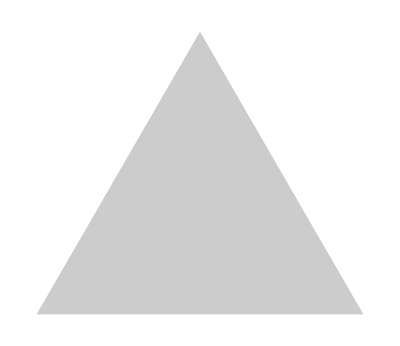
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Use Array to make a 10 by 10 grid where the leading diagonal and everything below it is 1 and the rest is 0. »

| Expected output: |  
  | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |

Q&A

What does # alone mean?

It’s equivalent to #1—a slot to be filled from the first argument of a function.

How does one say #1?

Either “slot 1” (reflecting its role in a pure function), or “hash 1” (reflecting how it’s written—the “#” is usually called “hash”).

Can one name arguments to a pure function?

Yes. It’s done with Function[{x,y},x+y], etc. It’s sometimes nice to do this for code readability, and it’s sometimes necessary when pure functions are nested.

Can Array make more deeply nested structures?

Yes—as deep as you want. Lists of lists of lists... for any number of levels.

What is functional programming?

It’s programming where everything is based on evaluating functions and combinations of functions. It’s actually the only style of programming we’ve seen so far in this book. In Section 38 we’ll see procedural programming, which is about going through a procedure and progressively changing values of variables.

Tech Notes

Fold gives the last element of FoldList, just like Nest gives the last element of NestList.

FromDigits reconstructs numbers from lists of digits, effectively doing what we used FoldList for above.

Accumulate[list] is FoldList[Plus,list].

Array and FoldList, like NestList, are examples of what are called higher-order functions, that take functions as input. (In mathematics, they’re also known as functionals or functors.)

You can set up pure functions that take any number of arguments at a time using # #, etc.

You can animate lists of images using ListAnimate, and show the images stacked in 3D using Image3D.

More to Explore

Guide to Functional Programming in the Wolfram Language »